```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY197/sec_int_data/500nm.dat"]
```

{{1.50189,0.259205},{1.45414,0.265973},{1.33983,0.288707},{1.30748,0.287807},{1.27821,0.299215},{1.24682,0.283448},{1.22351,0.252469},{1.20659,0.227454},{1.18213,0.182488},{1.16419,0.146694},{1.15263,0.132256},{1.13304,0.107957},{1.09662,0.314957},{1.09807,0.290952},{1.10207,0.293043},{1.10747,0.294683},{1.11401,0.295353},{1.12685,0.304908},{1.13867,0.314227},{1.15401,0.311081},{1.16573,0.294459},{1.20258,0.298399},{1.26466,0.292819},{1.30748,0.290204},{1.33983,0.261287},{1.37936,0.261672}}

0.228305+0.028809 x

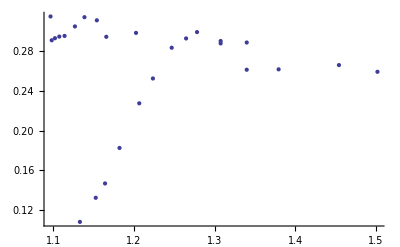

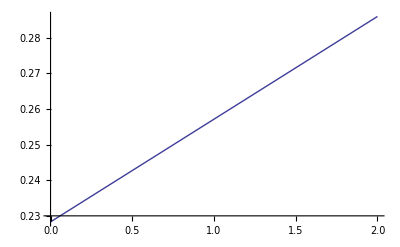

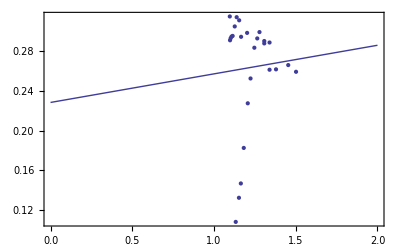

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```